#### Sezione d.

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[μ_,x_]:= μ x (1-x)
fn[μ_,x_,n_]:= Nest[f[μ,#]&,x,n]
```

```mathematica
(*Manipulate[ListPlot[fn[μ,0.4,#]&/@Range[100]],{μ,0,4}]*)
```

```mathematica
conf[μ_,n_,iterations_]:=Length[Union[Round[10^4(fnC[μ,0.4,iterations+#]-fnC[μ,0.4,iterations]),1]& /@Range[2^n]]]
```

```mathematica
data= ParallelTable[{μ,conf[μ,7,10000]},{μ,2.8,3.5,10^-6}];
```

$Aborted

```mathematica
fnC=Compile[{{μ,_Real},{x,_Real},{n,_Integer}},Nest[μ #(1-#)&,x,n]]
```

CompiledFunction[…]

per ottimizzare i tempi si può utilizzare un numero di iterazioni iniziale più basso (come per il numero di iterazioni utilizzate per cercare il punto) per trovare i primi punti e alzarlo man mano
questo processo si potrebbe automatizzare conoscendo più o meno dove sono i punti e regolando automaticamente il range di conseguenza

#### Troviamo i punti a manina:

```mathematica
databyhand=ParallelTable[{μ,conf[μ,#⟦1⟧,#⟦2⟧]},{μ,#⟦3⟧,#⟦4⟧,10^-6}]&/@{{2,200,2.8,3.1},{4,500,3.1,3.5},{5,1500,3.5,3.57},{6,10000,3.564,3.57},{7,30000,3.565,3.5702}}
```

#### con relativo check:

```mathematica
data0= ParallelTable[{μ,conf[μ,2,200]},{μ,2.8,3.1,10^-6}];
```

$Aborted

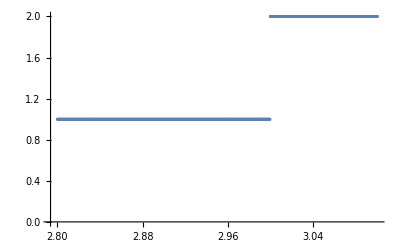

```mathematica
ListPlot[data0]
```

```mathematica
First@Last@Cases[data0,{_,1}]
```

2.9759

```mathematica
data1=ParallelTable[{μ,conf[μ,4,500]},{μ,3.1,3.5,10^-4}];
```

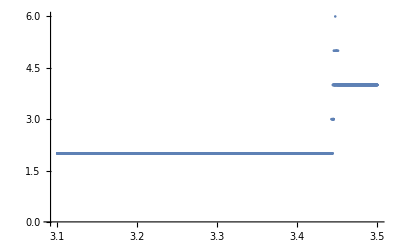

```mathematica
ListPlot[data1]
```

```mathematica
First@Last@Cases[data1,{_,2}]
```

3.4438

```mathematica
data2=ParallelTable[{μ,conf[μ,5,10]},{μ,3.5,3.57,10^-5}];
```

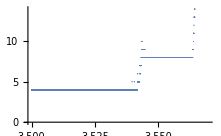

```mathematica
ListPlot[data2]
```

```mathematica
First@Last@Cases[data2,{_,4}]
```

3.54182

```mathematica
First@Last@Cases[data2,{_,8}]
```

3.56375

```mathematica
data3=ParallelTable[{μ,conf[μ,6,1]},{μ,3.564,3.57,10^-5}];
```

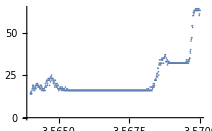

```mathematica
ListPlot[data3]
```

```mathematica
First@Last@Cases[data3,{_,16}]
```

3.5683

```mathematica
First@Last@Cases[data3,{_,32}]
```

3.56959

```mathematica
data4=ParallelTable[{μ,conf[μ,7,1]},{μ,3.565,3.5702,10^-6}];
```

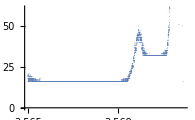

```mathematica
ListPlot[data4]
```

```mathematica
First@Last@Cases[data4,{_,64}]
```

3.56988

μ_∞≈3.57

```mathematica
data=Flatten[{data0,data1,data2,data3,data4},1];
```

#### da concludere

fare un data =Flatten[ {data_1,...,data_n}] o farlo computare un po’ con quella iniziale (o pi

```mathematica
μ[n_]:= First@Last@Cases[data,{_,2^n}]
```

```mathematica
feigenbaum =Table[(μ[n]-μ[n-1])/(μ[n+1]-μ[n]),{n,1,5}]
```

{4.76485,4.62997,4.56195,4.32122,4.69058}

eh. e mo?
tranne il quarto valore possiamo vedere che i numeri sono vicini

possiamo fare una media geometrica brutalmente

```mathematica
GeometricMean[Drop[feigenbaum,{4}]]
```

4.66124

ha senso farlo?
probabilmente nO! (ma sticazzi)
la costante è circa quella, con dati più precisi si potrebbe far meglio ma dovrei lavorarci sopra e sono pigro.

#### aumentiamo la precisione

Avendo calcolato approssimativamente una costante di Feigenbaum (= (μ_(n+1)-μ_n)/(μ_n-μ_(n-1))) ≈  4.67 e sapendo che μ_1≈3 μ_2≈3.45

facendo qualche conto vediamo che μ_(n+1)-μ_n= φ(μ_n-μ_(n-1)) ,quindi
 μ_(n+1)= (φ + 1)μ_n-φμ_(n-1) 
 ergo possiamo dire che range_n=[μ_n-ϵ, μ_n+ϵ ] utilizzando come φ il  4.67 calcolato in precedenza e calcolando ϵ come una percentuale di Δμ_n, facciamo il 50%

```mathematica
m[n_]:=5.67*m[n-1]-4.67*m[n-2]
m[0]:=0
m[1]:=3
m[2]:=3.45
```

costruirò una formula chiusa per m più tardi.

possiamo automatizzare il tutto facendo

```mathematica
moreprecisedatabyhand = ParallelTable[{μ,conf[μ,#⟦1⟧,#⟦2⟧]},{μ,#⟦3⟧,#⟦4⟧,10^-6}]&/@Table[{n+1,500 n^2,m[n]-(0.5(m[n]-m[n-1])),m[n]+(0.5(m[n+1]-m[n]))},{n,1,7}]
```

pociamo anche con g_μ(x)=μ sen(x)